## Preamble

```mathematica
δn[n_,H_,q_,d_]:=Table[Sum[((1+(ⅈ(2-q.n))/(d(1-q.n))(1-Exp[-ⅈ d(1-q.n)]))n⟦i⟧-(1+ⅈ/(d(1-q.n))(1-Exp[-ⅈ d(1-q.n)]))q⟦i⟧)(H⟦j,k⟧n⟦j⟧n⟦k⟧)/(2(1-q.n)),{j,1,3},{k,1,3}]-Sum[(1/2+ⅈ/(d(1-q.n))(1-Exp[-ⅈ d(1-q.n)]))H⟦i,j⟧n⟦j⟧,{j,1,3}],{i,1,3}]
δn[n_,H_,q_]:=Table[Sum[Sum[(n⟦i⟧-q⟦i⟧)(H⟦j,k⟧n⟦j⟧n⟦k⟧)/(2(1-q.n)),{k,1,3}]-1/2 H⟦i,j⟧n⟦j⟧,{j,1,3}],{i,1,3}]
```

```mathematica
SphericalIntegral[Integrand_,nSamplePoints_,nIntPoints_]:=Block[{IntegrandFunc,GaussLegendreNodesSampling,GaussLegendreNodesInt,GaussLegendreWeightsInt,IntegrandVals,FunctionVals},
IntegrandFunc=Compile[{{Θ,_Real},{θ,_Real},{ϕ,_Real}},Evaluate@Integrand];

GaussLegendreNodesSampling=Join[{-1},Sort[N[x/.Solve[LegendreP[nSamplePoints-2,x]==0]]],{1}];
GaussLegendreNodesInt=Sort[N[x/.Solve[LegendreP[nIntPoints,x]==0]]];
GaussLegendreWeightsInt=ParallelTable[2/((1-GaussLegendreNodesInt⟦i⟧^2)LegendrePDiff[nIntPoints,GaussLegendreNodesInt⟦i⟧]^2),{i,1,nIntPoints}];

IntegrandVals=ParallelTable[N[IntegrandFunc[ArcCos[GaussLegendreNodesSampling⟦i⟧],ArcCos[GaussLegendreNodesInt⟦j⟧],(k-(1/2))π/nIntPoints]],{i,1,nSamplePoints},{j,1,nIntPoints},{k,1,2nIntPoints}];

FunctionVals=Reverse@Table[{ArcCos[GaussLegendreNodesSampling⟦i⟧],ParallelSum[GaussLegendreWeightsInt⟦j⟧ IntegrandVals⟦i,j,k⟧,{j,1,nIntPoints},{k,1,2nIntPoints}]},{i,1,nSamplePoints}];

AbsMaxVal=Max@Abs@FunctionVals⟦All,2⟧;
FunctionVals⟦All,2⟧=FunctionVals⟦All,2⟧/AbsMaxVal;

Return[FunctionVals];]
```

```mathematica
n={0,0,1};
Subscript[n, x]={1,0,0};
Subscript[n, y]={0,1,0};
m={Sin[Θ],0,Cos[Θ]};
Subscript[m, θ]={Cos[Θ],0,-Sin[Θ]};
Subscript[m, ϕ]={0,1,0};
q=(1-ϵ){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
```

```mathematica
R=Simplify[RotationMatrix[-θ,{0,1,0}].RotationMatrix[-ϕ,{0,0,1}]];
```

```mathematica
y1=100;
y2=100;
```

```mathematica
epsilons={0,-0.1,-0.2,-0.5};
```

## Tensorial Modes Correlation Curves

```mathematica
Htensorial=Transpose[R].({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}}).R;

TensorialxθPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Htensorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Htensorial,q,y2]]];
Integrandxθ=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
SphericalIntegral[Integrandxθ,400,200],{i,1,4}];

TensorialyϕPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Htensorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Htensorial,q,y2]]];
Integrandyϕ=(Deltan.{0,1,0})(Deltam.{0,1,0});
SphericalIntegral[Integrandyϕ,400,200],{i,1,4}];
```

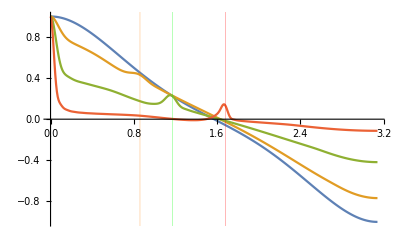

```mathematica
ListPlot[TensorialxθPlots,Joined->True,PlotRange->All,GridLines->{{{2*ArcCos[1/(1+0.1)],Orange},{2*ArcCos[1/(1+0.2)],Green},{2*ArcCos[1/(1+0.5)],Red}},None}]
```

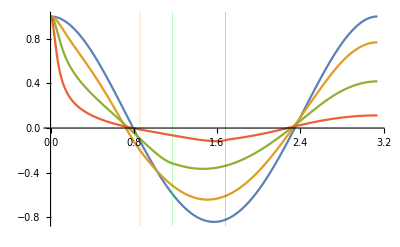

```mathematica
ListPlot[TensorialyϕPlots,Joined->True,PlotRange->All,GridLines->{{{2*ArcCos[1/(1+0.1)],Orange},{2*ArcCos[1/(1+0.2)],Green},{2*ArcCos[1/(1+0.5)],Red}},None}]
```

## Scalar Transverse Modes Correlation Curves

```mathematica
Hscalar=Transpose[R].({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}}).R;

ScalarxθPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hscalar,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hscalar,q,y2]]];
Integrandxθ=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
SphericalIntegral[Integrandxθ,400,200],{i,1,4}];

ScalaryϕPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hscalar,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hscalar,q,y2]]];
Integrandyϕ=(Deltan.{0,1,0})(Deltam.{0,1,0});
SphericalIntegral[Integrandyϕ,400,200],{i,1,4}];
```

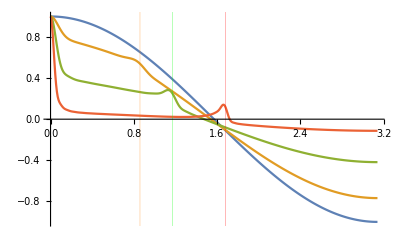

```mathematica
ListPlot[ScalarxθPlots,GridLines->{{{2*ArcCos[1/(1+0.1)],Orange},{2*ArcCos[1/(1+0.2)],Green},{2*ArcCos[1/(1+0.5)],Red}},None},Joined->True,PlotRange->All]
```

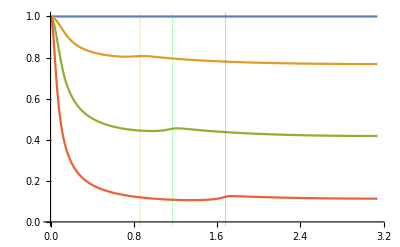

```mathematica
ListPlot[ScalaryϕPlots,Joined->True,PlotRange->All,GridLines->{{{2*ArcCos[1/(1+0.1)],Orange},{2*ArcCos[1/(1+0.2)],Green},{2*ArcCos[1/(1+0.5)],Red}},None}]
```

## Vectorial Modes Correlation Curves

```mathematica
Hvectorial=Transpose[R].({{0, 0, 1}, {0, 0, 1}, {1, 1, 0}}).R;

VectorialxθPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hvectorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hvectorial,q,y2]]];
Integrandxθ=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
SphericalIntegral[Integrandxθ,400,200],{i,1,4}];

VectorialyϕPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hvectorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hvectorial,q,y2]]];
Integrandyϕ=(Deltan.{0,1,0})(Deltam.{0,1,0});
SphericalIntegral[Integrandyϕ,400,200],{i,1,4}];
```

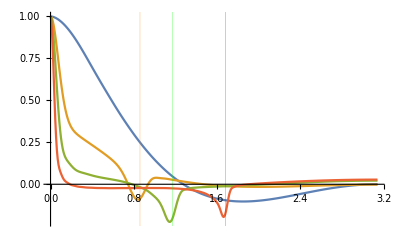

```mathematica
ListPlot[VectorialxθPlots,Joined->True,PlotRange->All,GridLines->{{{2*ArcCos[1/(1+0.1)],Orange},{2*ArcCos[1/(1+0.2)],Green},{2*ArcCos[1/(1+0.5)],Red}},None}]
```

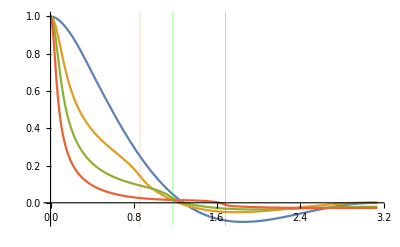

```mathematica
ListPlot[VectorialyϕPlots,Joined->True,PlotRange->All,GridLines->{{{2*ArcCos[1/(1+0.1)],Orange},{2*ArcCos[1/(1+0.2)],Green},{2*ArcCos[1/(1+0.5)],Red}},None}]
```

## Longitudinal Mode Correlation Curves

```mathematica
Hlongitudinal=√2 Transpose[R].({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}).R;

LongitudinalxθPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hlongitudinal,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hlongitudinal,q,y2]]];
Integrandxθ=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
SphericalIntegral[Integrandxθ,400,200],{i,1,4}];

LongitudinalyϕPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hlongitudinal,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hlongitudinal,q,y2]]];
Integrandyϕ=(Deltan.{0,1,0})(Deltam.{0,1,0});
SphericalIntegral[Integrandyϕ,400,200],{i,1,4}];
```

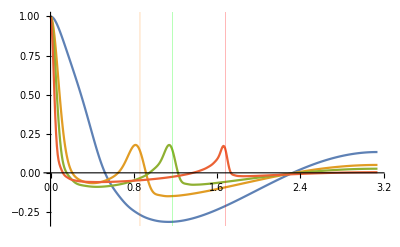

```mathematica
ListPlot[LongitudinalxθPlots,Joined->True,PlotRange->All,GridLines->{{{2*ArcCos[1/(1+0.1)],Orange},{2*ArcCos[1/(1+0.2)],Green},{2*ArcCos[1/(1+0.5)],Red}},None}]
```

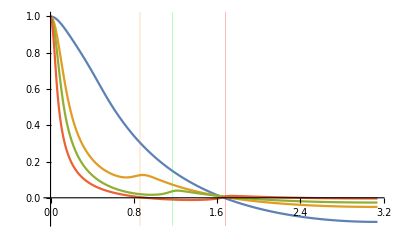

```mathematica
ListPlot[LongitudinalyϕPlots,Joined->True,PlotRange->All,GridLines->{{{2*ArcCos[1/(1+0.1)],Orange},{2*ArcCos[1/(1+0.2)],Green},{2*ArcCos[1/(1+0.5)],Red}},None}]
```

```mathematica
q=1.5{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Htensorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Htensorial,q,y2]]];
Integrand1[Θ_,θ_,ϕ_]=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
A=Table[{Θ,NIntegrate[Sin[θ]Integrand1[Θ,θ,ϕ],{θ,0,π},{ϕ,0,2π}]},{Θ,0,π,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.40622 and 1.97015×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31438 and 3.85279×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.25613 and 4.87117×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{0.,22.4547},{0.05,8.44323},{0.1,3.15977},{0.15,2.10152},{0.2,1.70785},{0.25,1.52253},{0.3,1.40622},{0.35,1.31438},{0.4,1.25613},{0.45,1.19521},{0.5,1.15096},{0.55,1.10211},{0.6,1.05726},{0.65,1.01394},{0.7,0.966078},{0.75,0.913203},{0.8,0.852665},{0.85,0.776776},{0.9,0.679901},{0.95,0.571038},{1.,0.455947},{1.05,0.336792},{1.1,0.216236},{1.15,0.102622},{1.2,-0.00488856},{1.25,-0.101407},{1.3,-0.173331},{1.35,-0.219335},{1.4,-0.219137},{1.45,-0.144453},{1.5,0.0311981},{1.55,0.39256},{1.6,1.1353},{1.65,2.92997},{1.7,1.85017},{1.75,-0.0251647},{1.8,-0.276718},{1.85,-0.406796},{1.9,-0.507625},{1.95,-0.597882},{2.,-0.683477},{2.05,-0.767788},{2.1,-0.851019},{2.15,-0.93496},{2.2,-1.02114},{2.25,-1.11158},{2.3,-1.21156},{2.35,-1.3276},{2.4,-1.45156},{2.45,-1.57665},{2.5,-1.69955},{2.55,-1.81765},{2.6,-1.92872},{2.65,-2.03306},{2.7,-2.12867},{2.75,-2.21507},{2.8,-2.29213},{2.85,-2.35946},{2.9,-2.41574},{2.95,-2.46262},{3.,-2.49866},{3.05,-2.52352},{3.1,-2.53778}}

```mathematica
A[[All,2]]=A[[All,2]]/A[[1,2]]
```

{1.,0.376012,0.140718,0.0935891,0.0760577,0.0678043,0.0626246,0.0585346,0.0559405,0.0532277,0.051257,0.0490814,0.0470841,0.0451551,0.0430235,0.0406687,0.0379727,0.034593,0.0302788,0.0254307,0.0203052,0.0149987,0.0096299,0.00457017,-0.000217708,-0.00451607,-0.00771914,-0.00976791,-0.00975909,-0.00643309,0.00138938,0.0174823,0.0505597,0.130484,0.0823955,-0.00112069,-0.0123234,-0.0181163,-0.0226066,-0.0266262,-0.030438,-0.0341928,-0.0378994,-0.0416376,-0.0454757,-0.0495032,-0.0539558,-0.0591235,-0.0646439,-0.0702148,-0.075688,-0.0809473,-0.085894,-0.0905406,-0.0947985,-0.0986462,-0.102078,-0.105077,-0.107583,-0.109671,-0.111276,-0.112383,-0.113018}